# Mathematica - Earthquake Data Plotting and Analysis

## Introduction

We have seen how plotting and visualizing data helps us to quickly analyse the data. In this project, I will demonstrate more about Geographic Data and Computation. I will also perform the analysis of Earthquake Data and estimate which areas are more prone to earthquakes.

## Geographic Data and Computation

### Descriptive Statistics

Median                                   The  Value below which are 50% of the observations.

Max                                          The maximum value in the data.

Min                                           The minimum value in the data.

1st Qu.                                     The value below which are 25% of the observations.

3st Qu.                                      The value below which are 75% of the observations.

### Plotting Basics

GeoGraphics                       Represents a two-dimensional geographical image.

GeoBackground                Option that specifies the background style of a GeoGraphics object.

GeoStyling                           Displays faces of polygons and other filled geo objects using mapstyle.

GeoRange                            Is an option for GeoGraphics and GeoStyling that specifies the range of latitude and longitude to include.

GeoIdentify                          Identifies the geographic entities of the type enttype in which the current geo location is contained.

GeoRegionValuePlot       Generates a plot in which the geographic subdivisions of reg are colored according to the values Entity[...,value]

GeoBounds                          Gives the ranges of latitudes and longitudes in the geo region g.

Entity                                      Represents an entity of specified type identified by name.

DateListPlot                         Plots the time series .

### Major world earthquakes recorded over the past 5 years

Mathematica has an inbuilt function defined as EarthquakeData[loc,mag,{start,end},property] which returns a time series for the specific earthquake property for earthquakes within the magnitude range mag during the time interval start to end. So, to plot the data recorded over the past 5 years with magnitude greater than or equal to 4, I selected loc -> All, mag -> 4, {start,end} -> {DateObject[{2013,10,31}],DateObject[{2018,10,31}] .
I then applied the Map function over this list to get both the Magnitude and the Position of each earthquake in the form List[{Magnitude,GeoPosition }]. After that, I used GeoGraphics to plot the data.

```mathematica
data={#["Magnitude"],#["Position"]}&/@Values[EarthquakeData[All,4,{DateObject[{2013,10,31}],DateObject[{2018,10,31}]}]]
GeoGraphics[{{Hue[0.7 (1-#1/9)],PointSize[0.0006 #1],Point[#2]}&@@@Sort[data]},GeoBackground->GeoStyling["ReliefMap"],GeoRange->All,ImageSize->{1200,600},PlotLabel->"Plot of Earthquake Magnitudes for the Entire World"]
```

{{5.2,GeoPosition[{-9.0734,119.606}]},{5.4,GeoPosition[{44.6376,124.081}]},{4.8,GeoPosition[{44.5661,124.215}]},{4.9,GeoPosition[{-18.6784,65.2599}]},{4.4,GeoPosition[{9.7989,124.236}]},33562,{4.,GeoPosition[{51.4654,-174.449}]},{4.4,GeoPosition[{-20.3979,-69.0003}]},{4.9,GeoPosition[{30.3711,87.5667}]},{4.6,GeoPosition[{6.0618,95.0842}]}}
 |  |  |  |

-Graphics-

### Earthquake Frequency By Country

Here,  I have selected magnitude as 6, the period from 01-01-2017 to 31-12-2017, property as “Position” and the location is set to All. So, the output will be the list of Positions where the earthquakes with magnitude >=6 have taken place. GeoIdentify[“Country”,x] identifies the Country in which the location x is contained. Tally lists all distinct elements together with their multiplicities. From the output we can clearly see that since Canada has a frequency of 3 (i.e. earthquake has occurred 3 times in the year 2017), it is coloured orange; Iran has a frequency of 4 and is coloured maroon; Russia has a frequency of 1 and is coloured yellow. One important point to note is that this plot doesn’t represent all the earthquakes occurred in 2017. If the earthquake occurred at GeoPosition[{0,-25.}], it won’t get displayed. This is because GeoIdentify[“Country”, GeoPosition[{0,-25.}]] will return empty as the location does not fall in any country.

```mathematica
locations=EarthquakeData[All,6,{DateObject[{2017,1,1}],DateObject[{2017,12,31}]},"Position"]["Values"];
countries=Tally[Flatten[Function[x,GeoIdentify["Country",x]]/@locations]]
GeoRegionValuePlot[countries,ImageSize->{1200,600},PlotLabel->"Earthquake Frequency Count per Country"]
```

EarthquakeData::dupdate: Earthquakes returned with duplicate dates, values may be combined.

{{Papua New Guinea,4},{Argentina,1},{Bolivia,1},{Russia,1},{Botswana,1},{Iran,4},{Chile,2},{Canada,3},{Indonesia,2},{Guatemala,2},{Philippines,3},{China,3},{North Korea,1},{Mexico,2},{Vanuatu,1},{Ecuador,1}}

-Graphics-

#### Tectonic Plates

We know that earth has 7 large plates and several other smaller plates. These plates are in constant motion and the movement of these plates is known as Plate Tectonics. This movement is the source of earthquakes and volcanos. This explains why the Geo-positions of EarthquakeData lie near the plate coordinates.

```mathematica
GeoGraphics[ResourceData["Large Global Plate Boundaries"][All,"Polygon"]]
```

The ResourceData Function returns Authentication error. So,I have downloaded the .wl file from the repository website and imported that data.(https://datarepository.wolframcloud.com/resources/Plate-Boundaries). I have also attached that file(Plate-Boundaries.wl).

```mathematica
data=Import["F:\\UCD Lecture Notes\\Mathematica for Research\\Plate-Boundaries.wl"];
GeoGraphics[data[All,"Polygon"],ImageSize->{1200,600},PlotLabel->"Tectonic plates"]
```

### Plot of Tectonic Plates and Earthquake Positions

I have combined both the above plots using Show[] function.

```mathematica
data={#["Magnitude"],#["Position"]}&/@Values[EarthquakeData[All,4,{DateObject[{2017,10,31}],DateObject[{2018,10,31}]}]];
data1=Import["F:\\UCD Lecture Notes\\Mathematica for Research\\Plate-Boundaries.wl"];
Show[GeoGraphics[{{Hue[0.7 (1-#1/9)],PointSize[0.0006 #1],Point[#2]}&@@@Sort[data]},GeoBackground->GeoStyling["ReliefMap"],GeoRange->All,ImageSize->{1200,600},PlotLabel->"Plot of earthquake positions and tectonic plates"],
GeoGraphics[{Thick,Red,data1[All,"Polygon"]},ImageSize->{1200,600}]]
```

-Graphics-

#### Frequency vs Magnitude Plot

I have considered only those earthquakes which were recorded in 2017 and had a magnitude of more than 3.5. The x-axis represents the months  and the y-axis represents the magnitude. The EarthquakeData returns a time series which is then passed as an input to the DateListPlot function.

EarthquakeData::dupdate: Earthquakes returned with duplicate dates, values may be combined.

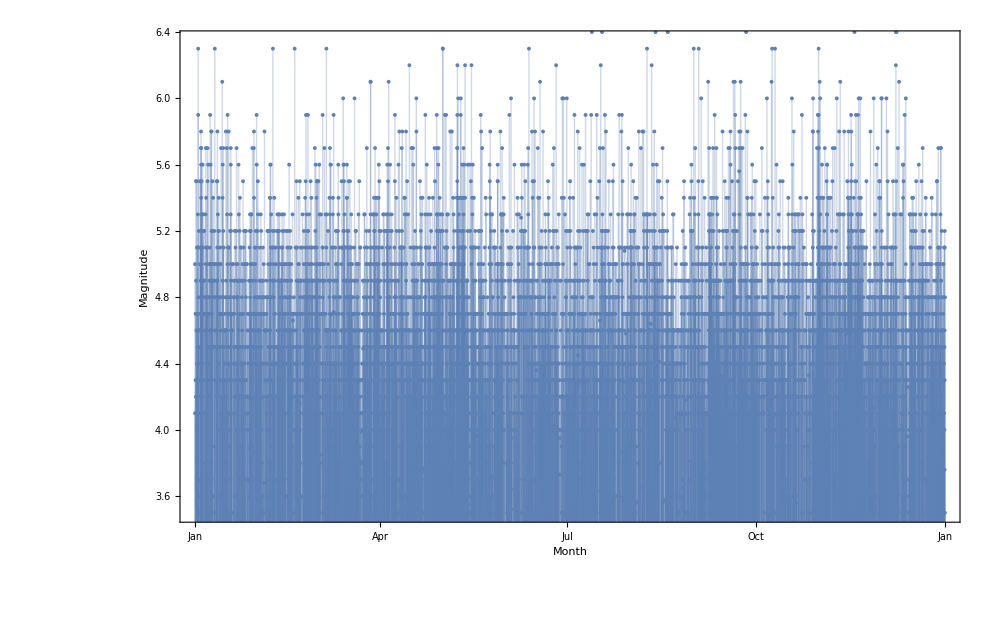

```mathematica
ed=EarthquakeData[All,3.5,{{2017,1,1},{2017,12,31}},"Magnitude"];
DateListPlot[ed,Joined->False,Filling->Axis,ImageSize->{1000,500},AxesLabel->{"Month","Magnitude"}]
```

#### Examine recorded earthquakes in the selected area:

Until now, we have plotted the Earthquake Data all around the world. In Mathematica, we can specify a particular region for consideration by using Entity[] Function. For e.g Entity[“Country”,”Ireland”] will take Ireland into consideration and Entity[“AdministrativeDivision”,{“California”,”UnitedStates”}] will consider California for analysis. Since India lies in the earthquake-prone area, the number of observations are higher. Here,magnitude =1, period from 01-01-2010 to 20-11-2018, MaxPlotPoints=300,Colour=Red

```mathematica
data=EarthquakeData[Entity["Country","India"], 4,{{2010,1,1},{2018,11,20}},"Position"]["Values"];
GeoGraphics[{GeoStyling["ReliefMap", MaxPlotPoints->300],Red,data/.GeoPosition[{x_,y_}]:>Point[{y,x}]},ImageSize->Large]
```

EarthquakeData::dupdate: Earthquakes returned with duplicate dates, values may be combined.

-Graphics-

#### Earthquake Density of India

Estimate Earthquake Densities
Map the density of earthquakes in India.

```mathematica
data=EarthquakeData[Entity["Country","India"],4,{{2010,1,1},{2018,11,20}},"Position"]["Values"];
{{latmin,latmax},{longmin,longmax}}=GeoBounds[Entity["Country","India"]];
𝒟=SmoothKernelDistribution[data[[All,1]],"SheatherJones"];
density=ContourPlot[Evaluate[PDF[𝒟,{y,x}]^(1/5)],{x,longmin,longmax},{y,latmin,latmax},Frame->False,PlotRange->{0.05,All},Contours->15,ColorFunction->(Directive[ColorData["TemperatureMap"][#],Opacity[0.5]]&),PlotRangePadding->None];
GeoGraphics[{GeoStyling[{"GeoImage",density}],Polygon[Entity["Country","India"]],Black,Opacity[0.2],PointSize[0.005],Point[Reverse/@data]},ImageSize->Large]
```

EarthquakeData::dupdate: Earthquakes returned with duplicate dates, values may be combined.

-Graphics-

#### Plot of Time period vs Magnitude of a selected region

Let’s say, we want to know more about the earthquakes occurring in the Pacific Ocean. No Entity can be defined specifically for that location and so to solve such cases, we can use Rectangle Function to locate our coordinates.
Eg: Rectangle[{xmin,ymin},{xmax,ymax}] represents an axis-aligned filled rectangle from {Subscript[x, min],Subscript[y, min]} to {Subscript[x, max],Subscript[y, max]}
In the below example, I have used Rectangle[{-85,39},{-95,42}] which specifies the x and the y coordinates for the Rectangle.
We can see that the frequency of earthquakes has increased significantly in recent times.

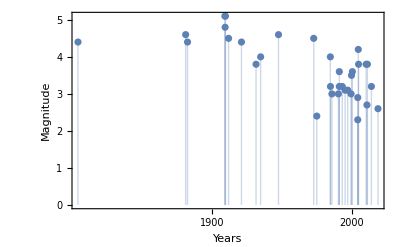

```mathematica
data=EarthquakeData[Rectangle[{-85,39},{-95,42}]];
DateListPlot[Values[{#["Period"],#["Magnitude"]}&/@data],Filling->0,Joined->False, AxesLabel->{"Years","Magnitude"}]
```

Similarly we can discover all known regions within a triangular region using polygon.

```mathematica
data=EarthquakeData[Polygon[GeoPosition[{{38.11,-100.24},{42.11,-100.24},{38.11,-109.24}}]]];
GeoGraphics[{Gray,Opacity[0.5],Polygon[GeoPosition[{{38.11,-100.24},{42.11,-100.24},{38.11,-109.24}}]],Red,Point[#["Position"]&/@Values[data]]},ImageSize->Large]
```

-Graphics-

#### Depth and position of Earthquakes around Japan

We can visualize the depth and the position of earthquakes using Graphics3D. The rectangle coordinates specify Japan’s x and y location, magnitude value is set to 5 and the period is set from 1st Jan 2010 to 1st Jan 2018.

```mathematica
data={#["Position"],#["Depth"]}&/@Values[EarthquakeData[Rectangle[{128,30},{147,46}],5,{{2010,1,1},{2018,1,1}}]];
Graphics3D[{Opacity[0.6],RGBColor[.6,.73,.36],Map[Append[Reverse[#],0]&,Entity["Country","Japan"]["Polygon"]/.GeoPosition->Identity,{-2}],RGBColor[.49,0,0],Opacity[0.6],Line[{Append[Reverse[First[#1]],0],Append[Reverse[First[#1]],-QuantityMagnitude[#2]/10]}&@@@data]},Axes->True,BoxRatios->{1,1,1/2},PlotLabel->"Depth vs position"]
```

-Graphics3D-

#### Depth and magnitude of Earthquakes around Japan

Similarly we can examine the recorded depths versus magnitudes of earthquakes in Japan for period from 1stJan 2010 to 1st Jan2018.

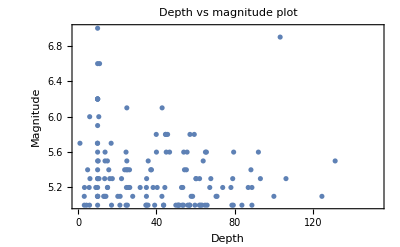

```mathematica
eq=Values[EarthquakeData[Polygon[Entity["Country","Japan"]],5,{{2010,1,1},{2018,1,1}}]];
depths=#["Depth"]&/@eq;
magnitudes=#["Magnitude"]&/@eq;
ListPlot[Transpose[{depths,magnitudes}],Axes->False,Frame->True,FrameLabel->{"Depth","Magnitude"},PlotLabel->"Depth vs magnitude plot"]
```

The largest magnitude registered within the time period.

```mathematica
Max[ed]
```

8.1

The frequency of the selected earthquakes as a function of their magnitude.

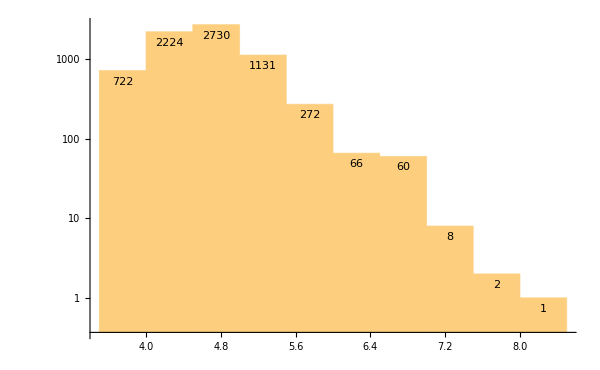

```mathematica
Histogram[ed,{3.5,8.5,0.5},ScalingFunctions->"Log",LabelingFunction->Top,ImageSize->600]
```

## Analysis

The main aim of our analysis is to find the locations (co-ordinates) which has the highest risk. I have considered 2 different approaches for analysis.

### 1) Linear Regression.

I have fetched the data for a random location of south-east region covering various islands. The latitudes and longitudes are specified in the Rectangle[] below.

```mathematica
data=EarthquakeData[Rectangle[{95,49},{130,-12}],4,{{2016,1,1},{2017,12,31}}];
```

```mathematica
eq=Values[data];
depths=#["Depth"]&/@eq;
magnitudes=#["Magnitude"]&/@eq;
geopos=#["Position"]&/@eq;
latitudes=Map[Latitude,geopos];
longitudes=Map[Longitude,geopos];
period=#["Period"]&/@eq;
dates=Map[DateList,period];
months=dates[[All,1]];
```

#### Descriptive Statistics

Summary of property ‘Depth’ :

```mathematica
Print["Mean=",Mean[depths]];
Print["Median=",Median[depths]];
Print["Max=",Max[depths]];
Print["Min=",Min[depths]]
Print["1st and 3rd quantiles",Quantile[depths,{1/4,3/4}]]
```

Mean=88.5773 km

Median=49.86 km

Max=627.35 km

Min=0. km

1st and 3rd quantiles{24.69 km,105.88 km}

Summary of ‘Magnitude’:

```mathematica
Print["Mean=",Mean[magnitudes]];
Print["Median=",Median[magnitudes]];
Print["Max=",Max[magnitudes]];
Print["Min=",Min[magnitudes]];
Print["1st and 3rd Quantiles=",Quantile[magnitudes,{1/4,3/4}]];
```

Mean=4.75778

Median=4.7

Max=7.3

Min=4.

1st and 3rd Quantiles={4.5,4.9}

Summary of ‘Latitude’:

```mathematica
Print["Mean=",Mean[latitudes]];
Print["Median=",Median[latitudes]];
Print["Max=",Max[latitudes]];
Print["Min=",Min[latitudes]];
Print["1st and 3rd Quantiles=",Quantile[latitudes,{1/4,3/4}]];
```

Mean=37.0841 °

Median=36.0214 °

Max=45.3351 °

Min=31.746 °

1st and 3rd Quantiles={34.8997 °,40.0745 °}

Summary of ‘Longitudes’ :

```mathematica
Print["Mean=",Mean[longitudes]];
Print["Median=",Median[longitudes]];
Print["Max=",Max[longitudes]];
Print["Min=",Min[longitudes]];
Print["1st and 3rd Quantiles=",Quantile[longitudes,{1/4,3/4}]];
```

Mean=138.28 °

Median=140.091 °

Max=145.743 °

Min=130.058 °

1st and 3rd Quantiles={135.638 °,141.211 °}

#### Fitting data using LinearModelFit

We have all the coordinate information, so lets plot that data on the graph. The x axis represents the longitudes and the y axis represents the latitudes.

```mathematica
newDta2=Transpose[{longitudes,latitudes}];
magn=QuantityMagnitude[Quantity[#,"AngularDegrees"]] &/@newDta2;
```

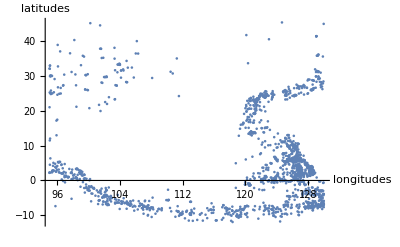

```mathematica
ListPlot[magn, AxesLabel->{"longitudes","latitudes"}]
```

To familiarize with the fitting problem, let’s consider a third - degree polynomial fit . Mathematica has an inbuilt function LinearModelFitpaclet:ref/LinearModelFit[{y_1,y_2,…},{f_1,f_2,…},x] that constructs a linear model of the form β_0+β_1 f_1+β_2 f_2+… that fits the y_i for successive x values 1, 2, ….The function returns the polynomial equation for the best curve fit.

```mathematica
newData=Transpose[{longitudes,latitudes}];
magn=QuantityMagnitude[Quantity[#,"AngularDegrees"]] &/@newData;
fit=LinearModelFit[magn,{1,x1,x1^2,x1^3},x1]["BestFit"]
```

5317.86-139.981 x1+1.22285 x1^2-0.0035435 x1^3

We plot the above equation with the coordinate points together and can see that the fitting curve almost matches the coordinates.

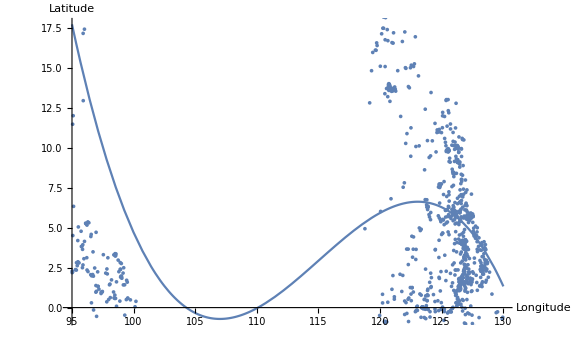

```mathematica
Show[Plot[fit,{x1,95,130}],ListPlot[magn],ImageSize->Large, AxesLabel->{"Longitude","Latitude"}]
```

#### Computing residuals

Let’s analyse it further.

The plot below is called as the comparison plot, where we have points whose first coordinate is the predicted value and the second coordinate the actual value. If the prediction was perfect, all the points would be on the  diagonal line. The closer the points are to the diagonal line, the better are the predictions.

```mathematica
xdata=magn[[All,1]];
ydata=magn[[All,2]];
```

Calculate the predicted values with the fit by substituting x1 values  :

```mathematica
ypred= fit/. x1->xdata;
```

The residuals are then differences between the actual y - components of the data and the corresponding predicted values :

```mathematica
residual=ydata-ypred;
```

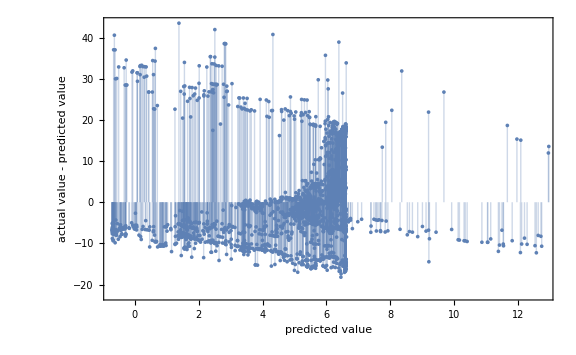

```mathematica
ListPlot[{ypred,residual}ᵀ,Filling->Axis,Frame->{True,True,False,False},FrameLabel->{"predicted value","actual value - predicted value"},ImageSize->Large]
```

On the x - axis, we have the predicted values and, on the y- axis, the residuals(actual value - predicted values). The root mean square error (RMSE) is

```mathematica
RootMeanSquare[residual]
```

12.1385

#### Comparing the best fit equation.

In the above LinearModelFit[] function, I have specified the degree of the polynomial to be 3. Lets compare the results if the degree is 1,2,3 or 4. We can conclude that there is not much difference in the curve when the degree > 3

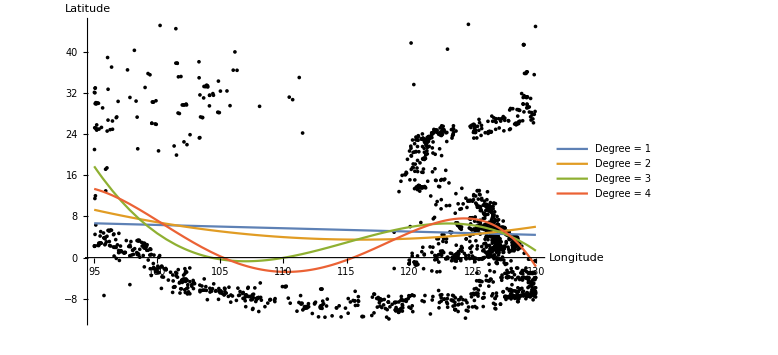

```mathematica
fits=Table[LinearModelFit[magn,Table[x1^i,{i,0,d}],x1]["BestFit"],{d,4}];
Show[ListPlot[magn,PlotStyle->Black],Plot[Evaluate@fits,{x1,95,130},PlotLegends->{"Degree = 1","Degree = 2","Degree = 3","Degree = 4"}],ImageSize->Large, AxesLabel->{"Longitude","Latitude"}]
```

### 2)Cluster Analysis.

The second approach is the cluster analysis. The basic idea is that we divide the coordinates into a set of clusters and then we compute the cluster mean. The coordinates of this cluster mean is nothing but the highest risk point.
Here, I have decided to divide my data into 6 different clusters. Now, to find clusters, Mathematica has a function defined as FindClusters[x,y] where x represents the points and y represents the no. of clusters that you want. As we can see from the plot below that there are 6 different clusters each represented by a different colour.

```mathematica
x=FindClusters[magn,6];
```

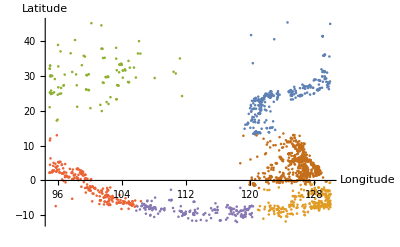

```mathematica
ListPlot[x, AxesLabel->{"Longitude","Latitude"}]
```

#### Cluster Mean

The next task is to compute the cluster mean.

```mathematica
Map[Mean,x]
```

{{123.642,23.3165},{127.448,-6.22927},{100.484,29.8529},{99.9743,-1.29075},{113.72,-8.63356},{125.743,4.15941}}

#### Plotting Cluster Mean and Cluster points

Lets plot the cluster points along with the cluster mean which we have calculated just now. The “M” in the graph represents the cluster Mean. These newly calculated coordinates have the highest risk of earthquakes, or in other words these locations are more prone to earthquakes.

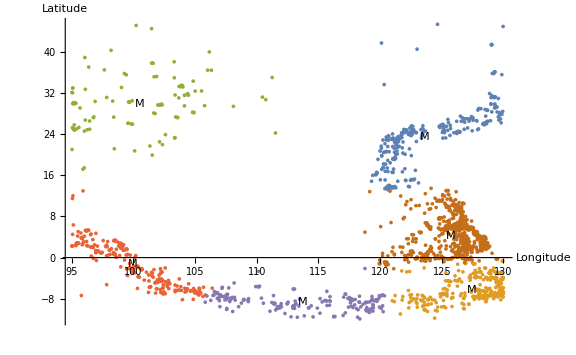

```mathematica
Show[ListPlot[x],ListPlot[Map[Mean,x],PlotMarkers->{"M"},PlotStyle->Black],ImageSize->Large, AxesLabel->{"Longitude","Latitude"}]
```

## Conclusion

Mathematica has a lot to offer when it comes to data analysis and plotting. I have explored only linear regression and cluster analysis. I believe that there may be more inbuilt functions which could have helped me significantly for this project.